# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

## Regression

```mathematica
gaussReg[xdata_,ydata_,dydata_]:=With[{Δ=Total[1/#^2&/@ dydata]Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[xdata]}])^2},{1/Δ(Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}] Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), 1/Δ(Total[1/#^2&/@ dydata]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), Sqrt[1/Δ Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]], Sqrt[1/Δ Total[1/#^2&/@ dydata]]} ]
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

```mathematica
combinedReg[xdata_,ydata_,dydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σa,σb,σ},Δ=(n sx2-sx^2);{a,b,σa,σb}=gaussReg[xdata,ydata, dydata];σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,Max[σa,σ Sqrt[sx2/Δ]],Max[σb,σ Sqrt[n/Δ]]}]
```

## Errors

```mathematica
σv=0.025;
σP=0.25;
```

## Plotting

```mathematica
cutData=DeleteCases[x_/;x[[3]]!="Gemischt"]/@data;
```

```mathematica
meanData=10^5 Mean[#[[All,2]]]&/@cutData;
```

```mathematica
errorMeanData=10^5 σP/Sqrt[Length[#]]&/@cutData;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
logData=Log[meanData]
dlogData=Table[errorMeanData[[i]]/meanData[[i]],{i,1,Length[meanData]}]
```

{14.7129,14.7886,14.8387,14.899,14.9459,15.0073,15.0454,15.0411,15.0654,15.0683,Log[100000 Mean[{}]],Log[100000 Mean[{}]],Log[100000 Mean[{}]]}

{0.00360309,0.00262031,0.00339634,0.00267536,0.00285411,0.00286958,0.00298354,0.00366972,0.00320354,0.00714286,ComplexInfinity,ComplexInfinity,ComplexInfinity}

```mathematica
fitData=Transpose[{1/(temps+273.15),logData}][[1;;-4]]
```

{{0.00329761,14.7129},{0.00327172,14.7886},{0.00324517,14.8387},{0.00321802,14.899},{0.00319234,14.9459},{0.00317309,15.0073},{0.00315209,15.0454},{0.00314713,15.0411},{0.00314218,15.0654},{0.00313725,15.0683}}

```mathematica
errorFitDatay=dlogData[[1;;-4]]
```

{0.00360309,0.00262031,0.00339634,0.00267536,0.00285411,0.00286958,0.00298354,0.00366972,0.00320354,0.00714286}

```mathematica
pars=gaussReg[fitData[[All,1]],fitData[[All,2]],errorFitDatay]
```

{21.9324,-2185.83,0.062219,19.4165}

```mathematica
LinearModelFit[fitData,x,x,Weights->1/errorFitDatay^2]["ParameterTableEntries"]
```

{{21.9324,0.162767,134.747,1.02891×10^-14},{-2185.83,50.7942,-43.0332,9.37674×10^-11}}

```mathematica
LinearModelFit[fitData,x,x,Weights->1/errorFitDatay^2]["RSquared"]
```

0.995699

```mathematica
Table[Around[logData[[i]],dlogData[[i]]],{i,1,Length[logData]}]
```

{14.7130.004,14.78860.0026,14.83870.0034,14.89900.0027,14.94590.0029,15.00730.0029,15.04540.0030,15.0410.004,15.06540.0032,15.0680.007,Log[100000 Mean[{}]]ComplexInfinity,Log[100000 Mean[{}]]ComplexInfinity,Log[100000 Mean[{}]]ComplexInfinity}

```mathematica
pars[[2]]*8.314
pars[[4]]*8.314
```

-18173.

161.429

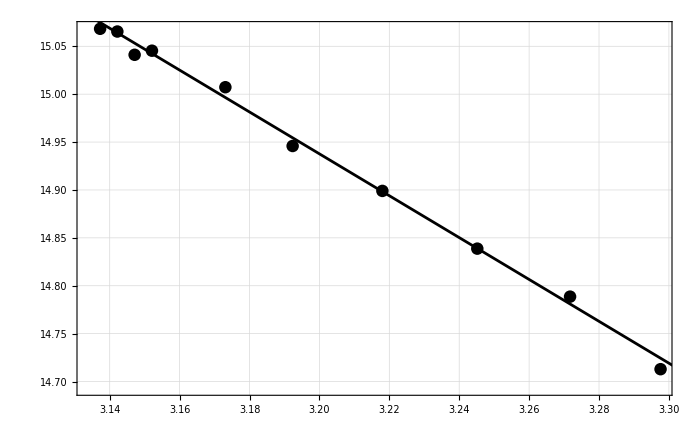

```mathematica
Show[ListPlot[{#[[1]]*10^3,#[[2]]}&/@fitData,PlotStyle->Black],Plot[pars[[1]]+pars[[2]](x/10^3),{x,0,4},PlotStyle->Black],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig2.pdf",Show[ListPlot[{#[[1]]*10^3,#[[2]]}&/@fitData,PlotStyle->Black],Plot[pars[[1]]+pars[[2]](x/10^3),{x,0,4},PlotStyle->Black],pltsettings],Background->None];
```

## Endpunkt der Kurve

```mathematica
Exp[pars[[1]]+pars⟦2⟧/(45.6+273.15)]
```

3.5231×10^6

```mathematica
Around[pars[[1]],pars[[3]]]
Around[pars[[2]],pars[[4]]]
```

21.930.06

-2186.19.

```mathematica
Sqrt[(pars[[3]] Exp[pars[[1]]+pars⟦2⟧/(45.6+273.15)] )^2 +(pars⟦4⟧/(45.6+273.15) Exp[pars[[1]]+pars⟦2⟧/(45.6+273.15)])^2]
```

306769.

## Verdampfungsenthalpie

dp/dT = ΔH/(ΔV T)

```mathematica
pressureData=meanData[[1;;-4]];
tempData=temps[[1;;-4]];
```

```mathematica
derivatives=NDSolve`FiniteDifferenceDerivative[1, tempData,pressureData,DifferenceOrder->4]
```

{119227.,56673.9,58718.3,57008.1,88038.5,101345.,-73394.6,105412.,172227.,-231819.}

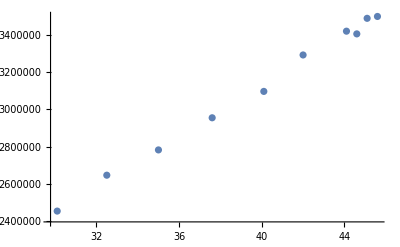

```mathematica
ListPlot[Transpose[{tempData,pressureData}]]
```

```mathematica
(Max[#[[All,1]]]-Min[#[[All,1]]]&)/@cutData
```

{0.7,0.6,0.5,0.45,0.4,0.3,0.25,0.15,0.2,0.,-∞,-∞,-∞}

```mathematica
ΔV=10^(-6)(Max[#[[All,1]]]-Min[#[[All,1]]]&)/@cutData[[1;;-4]]
```

{7.×10^-7,6.×10^-7,5.×10^-7,4.5×10^-7,4.×10^-7,3.×10^-7,2.5×10^-7,1.5×10^-7,2.×10^-7,0.}

```mathematica
ΔH=Table[ derivatives[[i]] (temps[[i]]+273.15) ΔV[[i]],{i,1,Length[derivatives]}]
```

{25.309,10.3934,9.04702,7.97187,11.0312,9.58162,-5.82111,5.02421,10.9622,0.}

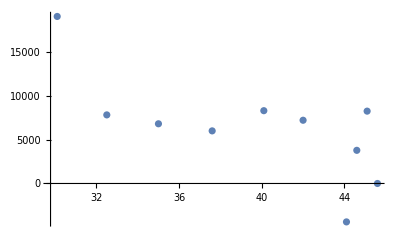

```mathematica
ListPlot[Transpose[{tempData, ΔH/0.0013301447593711529}]]
```